```mathematica
(* First time MaTeX config, don't run *)
Needs["PacletManager`"]
ResourceFunction["MaTeXInstall"][](* Tex instalation and Ghostscript required*)
ConfigureMaTeX["pdfLaTeX" -> "C:\\Users\\Sergio\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe", "Ghostscript"->"C:\\Program Files\\gs\\gs10.04.0\\bin\\gswin64c.exe"]
```

PacletObject[…]

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Sergio\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.04.0\bin\gswin64c.exe}

```mathematica
Needs["MaTeX`"] (* everytime load MaTeX for TeX and test it. !! run from here or the next cell*)
<<MaTeX`
MaTeX["x^2 + \\sin(x)"]
```

-Graphics-

```mathematica
(* values provided for the model *)
constPSI = -1.43 *(10^-3) (* KPa --> MPa *)
a = 8
b=5.39
c = 2+2.5*b
Ks = 20 *(10000   /   (60*60*24)) (* using loomy sand for now and making cm/d --> microm/s *)
dr =6*(10^-4)  (* m root diameter *)
Zr=0.6  (* m rooting depth, should we use the 75% of it? *)
RAIw=5 
RAI = 9.8 (*m^2/m^2 so dimentionless *)
gsrsat = 0.047  (* m / s MPa *)
LAI = 1.4
lsr= Sqrt[dr*Zr/RAI] * (10^6)  (* m --> microm *)
psillist ={0.0,0.1,0.2, 0.3, 0.4, 0.5, 0.6, 0.7} 
k1 = 0.005 (* m^2/W *)
k2 = 0.0016 (* 1/K^2 *)
Topt = 298 (* K *)
psil0 = -4.5 (* MPa *)
psil1 = -0.05 (* MPa *)
Dx = 0.0077 (* g /kg -->kg/kg *)
RH=0.4  (* percentage as a number from 0 to 1 *)
R = 8.314 (* m^3 Pa / K mol *)
vw = 18*(10^-6) (* m^3/mol *)
p0=0.1013 * 10^6 (* MPa --> Pa*)
gamma = 9.81 (* kg /m^3 *)
gammaw = 9800 *(1/10^12) (* gammaw=g*rhow units  Kg/m^2 s^2 --> kg / microm^2 s^2 *)
rho =1.23 (* kg/m^3 *)
rhow = 998 (* kg/m^3 *)
g =9.8 (* m^2/s *)
cp = 1012 (* Pa m^3 / kg K *)
ga =20 *(10^3)(* mm/s --> microm /s*)
gsmax =25*(10^3) (* mm/s -- microm/s *)
gpmax =11.7 (* vulnerability curve microm/MPa s*)
cv=2
dv=2
phi=400 (* W/m^2 *)
```

-0.00143

8

5.39

15.475

125/54

3/5000

0.6

5

9.8

0.047

1.4

6060.92

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7}

0.005

0.0016

298

-4.5

-0.05

0.0077

0.4

8.314

9/500000

101300.

9.81

49/5000000000

1.23

998

9.8

1012

20000

25000

11.7

2

2

400

```mathematica
(*  RAI[s_] =RAIw* s^a    we'll use the constant RAI from the table*)
```

```mathematica
Evap[gsrp_, psis_,psil_]= gsrp * (psis-psil)
```

gsrp (-psil+psis)

```mathematica
K[s_]= Ks*s^c
```

(125 s^15.475)/54

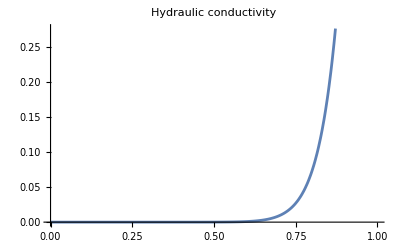

```mathematica
Plot[
K[s],{s,0,1},
PlotLabel->"Hydraulic conductivity",
AxesLabel->{MaTeX["s"],MaTeX["K (\\mu m/s)"]} ]
```

```mathematica
gsrp[gsr_, gp_]= (gsr*gp*LAI)/(gsr+LAI*gp) (*microm /s MPa*)
gsr[K_] = K/(gammaw*lsr)  (*microm /s MPa*)
gs[fphi_ ,fTa_, fpsil_,fD_]= gsmax*fphi*fTa*fpsil*fD 
gp[psil_]=gpmax*Exp[-((-psil/dv)^cv)] (*microm/s MPa*)
gsa[gs_,ga_]=(gs*ga)/(gs+ga)
(*use constant ga*)
```

(1.4 gp gsr)/(1.4 gp+gsr)

16835.9 K

25000 fD fphi fpsil fTa

11.7 ⅇ^(-psil^2/4)

(20000 gs)/(20000+gs)

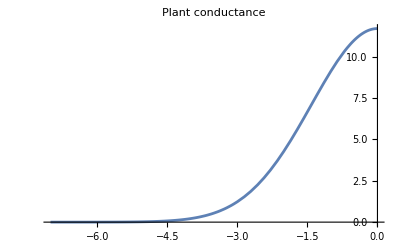

```mathematica
Plot[
gp[psil],{psil,-7,0},
PlotLabel->"Plant conductance",
AxesLabel->{MaTeX["\\psi_l"],MaTeX["g_p (\\mu m/Mpa\cdot s)"]} ]
```

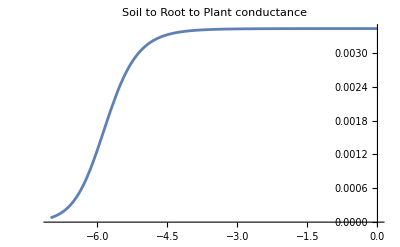

```mathematica
Plot[ 
gsrp[gsr[K[0.35]],gp[psil]],{psil,-7,0},
PlotLabel->"Soil to Root to Plant conductance",
AxesLabel->{MaTeX["\\psi_l"],MaTeX["g_{srp} (\\mu m/Mpa\cdot s)"]} ]
```

```mathematica
fphi[phi_]= 1-Exp[-k1*phi]
fTa[Ta_]=1-k2*(Ta-Topt)^2
fpsil[psil_]=Piecewise[{{(psil-psil0)/(psil1-psil0), psil0<=psil<=psil1},{0,psil<psil0}},1]
fD[D_]= 1 / (1 + (D/Dx))
```

0.864665

1-0.0016 (-298+Ta)^2

Piecewise[{{0.224719 (4.5+psil), -4.5≤psil≤-0.05}, {0, psil<-4.5}, {1, True}}]

1/(1+129.87 D)

```mathematica
esat[T_]=6.1094*Exp[17.625*(T-273.15)/(T-30.11)] * (10^-4) (* hPa --> MPa *)
```

0.00061094 ⅇ^((17.625 (-273.15+T))/(-30.11+T))

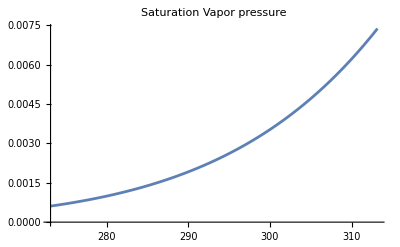

```mathematica
Plot[
esat[T],{T,0+273.15,40+273.15},
PlotLabel->"Saturation Vapor pressure",
AxesLabel->{MaTeX["T (K)"],MaTeX["e_{sat} (Mpa)"]} ]
```

```mathematica
ea[T_] =RH*esat[T]
```

0.000244376 ⅇ^((17.625 (-273.15+T))/(-30.11+T))

```mathematica
VPD[T_]= esat[T]-ea[T]
```

0.000366564 ⅇ^((17.625 (-273.15+T))/(-30.11+T))

0.000366564 ⅇ^((17.625 (-273.15+T))/(-30.11+T))

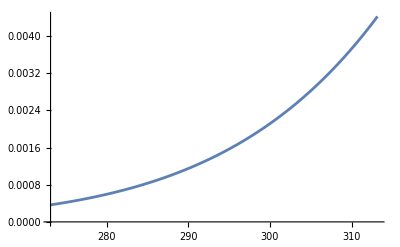

```mathematica
0.000366564 ⅇ^((17.625 (-273.15+T))/(-30.11+T))
Plot[VPD[T],{T,273.15,313.15}]
```

```mathematica
el[T_,esat_,psil_]=esat*Exp[(vw*(psil-g*rhow*Zr))/(R*T)]
```

ⅇ^((2.16502×10^-6 (-5868.24+psil))/T) esat

```mathematica
(* Jarvis function plots *)
fphiplot=Plot[
fphi[phi],{phi,0,800},
PlotLabel->MaTeX["f_\\phi(\\phi)"],
AxesLabel->{MaTeX["\\phi"],MaTeX["f_\\phi"]} ];
fTaplot=Plot[
fTa[Ta], {Ta,273.15,313.15},
PlotLabel->MaTeX["f_{T_a}(T_a)"],
AxesLabel->{MaTeX["T_a"],MaTeX["f_{T_a}"]} ];
fDplot=Plot[
fD[D],{D,0,0.05},
PlotLabel->MaTeX["f_{D}(D)"],
AxesLabel->{MaTeX["D"],MaTeX["f_{D}"]} ];
fpsilplot=Plot[
fpsil[psil],{psil, -7,2},
PlotLabel->MaTeX["f_{\\psi_l}(\\psi_l)"],
AxesLabel->{MaTeX["\\psi_l"],MaTeX["f_{\\psi_l}"]} ];
```

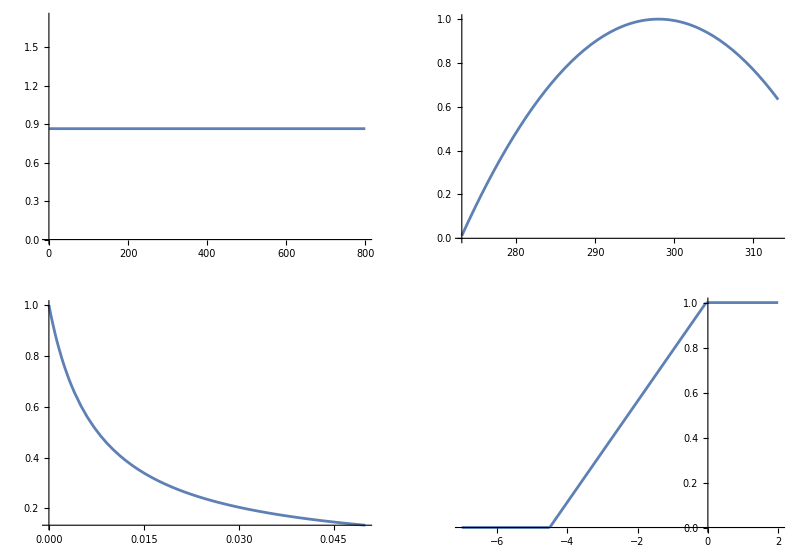

```mathematica
GraphicsGrid[{{fphiplot,fTaplot},{fDplot,fpsilplot}}]
```

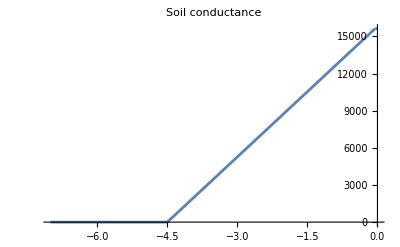

```mathematica
Plot[
gs[fphi[phi] ,fTa[303], fpsil[psil],fD[VPD[303]]],{psil,-7,0},
PlotLabel->"Soil conductance",
AxesLabel->{MaTeX["\\psi_l"],MaTeX["g_s (\\mu m/Mpa\cdot s)"]} ]
```

```mathematica
psis[s_]= constPSI*s^(-b) 
psia[a_]= ((R*T/vw)Log[RH] + gammaw*Zr ) * (10^-6) (* Mpa conversion *)
```

-0.00143/s^5.39

(5.88×10^-9-423225. T)/1000000

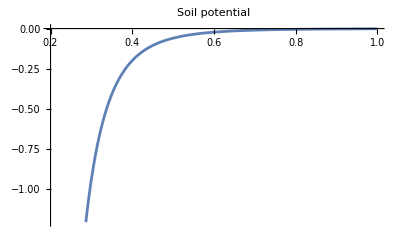

```mathematica
Plot[
psis[s],{s,0.2,1},
PlotLabel->"Soil potential",
AxesLabel->{MaTeX["s"],MaTeX["\\psi_s (MPa)"]} ]
```

```mathematica
Efinal[psil_,s_]=gsrp[gsr[K[s]], gp[psil]]*(psis[s]-psil)
E2final[psil_,T_]= (rho/rhow)*gsa[gs[fphi[phi] ,fTa[T], fpsil[psil],fD[VPD[T]]], ga]*(0.622/p0)*(
el[T,esat[T],psil]- ea[T])
```

(638360. ⅇ^(-psil^2/4) (-psil-0.00143/s^5.39) s^15.475)/(16.38 ⅇ^(-psil^2/4)+38971.9 s^15.475)

(3.2717 (0.00061094 ⅇ^((17.625 (-273.15+T))/(-30.11+T)+(2.16502×10^-6 (-5868.24+psil))/T)-0.000244376 ⅇ^((17.625 (-273.15+T))/(-30.11+T))) (1-0.0016 (-298+T)^2) (Piecewise[{{0.224719 (4.5+psil), -4.5≤psil≤-0.05}, {0, psil<-4.5}, {1, True}}]))/((1+0.0476057 ⅇ^((17.625 (-273.15+T))/(-30.11+T))) (20000+(21616.6 (1-0.0016 (-298+T)^2) (Piecewise[{{0.224719 (4.5+psil), -4.5≤psil≤-0.05}, {0, psil<-4.5}, {1, True}}]))/(1+0.0476057 ⅇ^((17.625 (-273.15+T))/(-30.11+T)))))

```mathematica
E35=Plot[Efinal[psil,0.35],{psil,-7,0}];
E40=Plot[Efinal[psil,0.40],{psil,-7,0}];
E293 = Plot[E2final[psil,293],{psil,-7,0}];
E298 = Plot[E2final[psil,298],{psil,-7,0}];
E303 = Plot[E2final[psil,303],{psil,-7,0}];
E308 = Plot[E2final[psil,308],{psil,-7,0}];
E313 = Plot[E2final[psil,313],{psil,-7,0}];
E318 = Plot[E2final[psil,318],{psil,-7,0}];
```

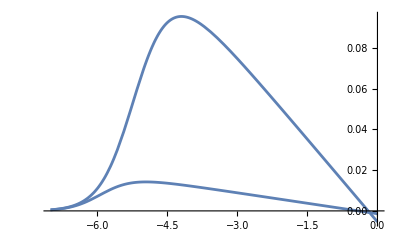

```mathematica
Show[E35,E40, PlotRange->All]
```

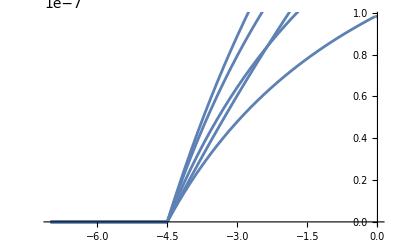

```mathematica
Show[E293,E298,E303,E308,E318]
```